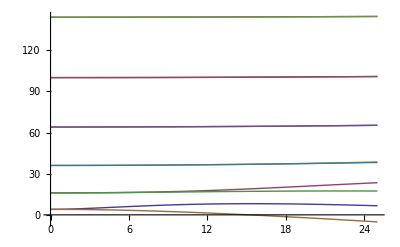

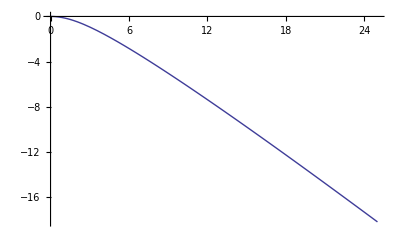

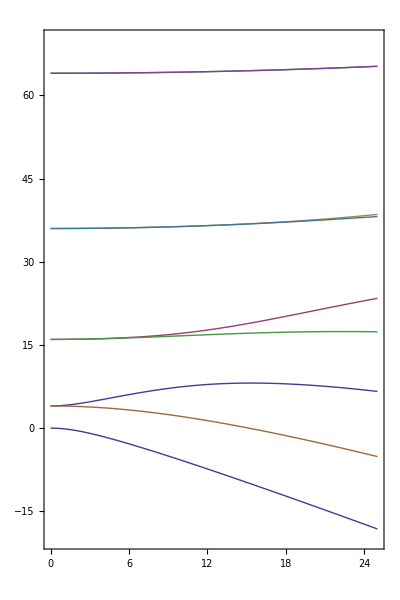

List

```mathematica
nmax=6;
kappastart=0.0;
kappaend=25.0;
eigenplotsA=Table[MathieuCharacteristicA[2*i,kappa/2.0],{i,1,nmax}];
eigenplotsB=Table[MathieuCharacteristicB[2*i,kappa/2.0],{i,1,nmax}];
eigenplots=Join[eigenplotsA,eigenplotsB];
p1=Plot[eigenplots,{kappa,kappastart,kappaend}]
p2=Plot[MathieuCharacteristicA[0,kappa/2.0],{kappa,kappastart,kappaend}]
Show[p1,p2,PlotRange->{-20,70},Frame->True,AspectRatio->1.5]
```